```mathematica
SetDirectory["C:\\Users\\Lion\\Documents\\My Projects\\GOT\\Extract txt\\Castles"]
```

C:\Users\Lion\Documents\My Projects\GOT\Extract txt\Castles

```mathematica
Directory[]
```

C:\Users\Lion\Documents\My Projects\GOT\Extract txt\Castles

```mathematica
FileNames[]
```

{CastlesBaratheon.txt,CastlesGJ.txt,CastlesLannister.txt,CastlesMartell.txt,CastlesStark.txt,CastlesTyrell.txt}

```mathematica
castlesStark=Import["CastlesStark.txt","Table","FieldSeparators"->","];
castlesMartell=Import["CastlesMartell.txt","Table","FieldSeparators"->","];
castlesTyrell=Import["CastlesTyrell.txt","Table","FieldSeparators"->","];
castlesGJ=Import["CastlesGJ.txt","Table","FieldSeparators"->","];
castlesLannister=Import["CastlesLannister.txt","Table","FieldSeparators"->","];
castlesBaratheon=Import["CastlesBaratheon.txt","Table","FieldSeparators"->","];
```

```mathematica
ST=Transpose[castlesStark][[2]]+Transpose[castlesStark][[3]];
BA=Transpose[castlesBaratheon][[2]]+Transpose[castlesBaratheon][[3]];
MA=Transpose[castlesMartell][[2]]+Transpose[castlesMartell][[3]];
TY=Transpose[castlesTyrell][[2]]+Transpose[castlesTyrell][[3]];
GJ=Transpose[castlesGJ][[2]]+Transpose[castlesGJ][[3]];LA=Transpose[castlesLannister][[2]]+Transpose[castlesLannister][[3]];
```

```mathematica
(Transpose[castlesStark][[1]]+Transpose[castlesMartell][[1]]+Transpose[castlesTyrell][[1]]+Transpose[castlesGJ][[1]]+Transpose[castlesLannister][[1]]+Transpose[castlesBaratheon][[1]])/6-Transpose[castlesBaratheon][[1]]
```

```mathematica
Transpose[{Transpose[castlesStark][[1]],LA,MA,TY,GJ,ST,BA}]>>"EndCastles.txt"
```

```mathematica
Directory[]
```

C:\Users\Lion\Documents\My Projects\GOT\Extract txt\Castles

```mathematica
castles=<<"EndCastles.txt";
castlesmean=Mean[Cases[castles,{#,_Integer,_Integer,_Integer,_Integer,_Integer,_Integer}][[1,2;;7]]&/@list];
castlesdev=MeanDeviation[Cases[castles,{#,_Integer,_Integer,_Integer,_Integer,_Integer,_Integer}][[1,2;;7]]&/@list];
mean=Transpose[{castlesmean}];
```

```mathematica
mean
```

{{11/5},{7/2},{11/5},{17/5},{4},{19/5}}

```mathematica
list=Transpose[castles][[1]][[;;]];
```

```mathematica
Transpose[{castlesmean,castlesdev}]
```

{{4,3},{9/2,5/2},{3/2,3/2},{3,2},{3,1},{7/2,1/2}}

```mathematica
names
```

{Lennister,Martell,Tyrell,Graufreud,Stark,Baratheon}

```mathematica
Needs["ErrorBarPlots`"]
games2castles[pos_]:=(
SetDirectory["C:\\Users\\Lion\\Documents\\My Projects\\GOT\\Extract txt\\Castles"];
castles=<<"EndCastles.txt";
castlesmean=Mean[Cases[castles,{#,_Integer,_Integer,_Integer,_Integer,_Integer,_Integer}][[1,2;;7]]&/@pos];
castlesdev=StandardDeviation[Cases[castles,{#,_Integer,_Integer,_Integer,_Integer,_Integer,_Integer}][[1,2;;7]]&/@pos];
names={"Lennister","Martell","Tyrell","Graufreud","Stark","Baratheon"};
namesen={"Lannister","Martell","Tyrell","Greyjoy","Stark","Baratheon"};
mean=Flatten[Transpose[{castlesmean}]];
Show[BarChart[mean,ChartLabels->namesen,ChartStyle->{Red, Orange, Green, Black,White,Yellow},PlotLabel->StringForm["From `` Games",Length[castles]],Frame->True,FrameLabel->{None,"#Castles"},ImageSize->Large],ErrorListPlot[Transpose[{castlesmean,castlesdev}],PlotRange->{Automatic,{0,7}},PlotStyle->{Gray,Dashed}]]
)
```

```mathematica
Transpose[{castlesmean,castlesdev}]
```

{{11/5,47/25},{7/2,13/10},{11/5,6/5},{17/5,58/25},{4,9/5},{19/5,8/5}}

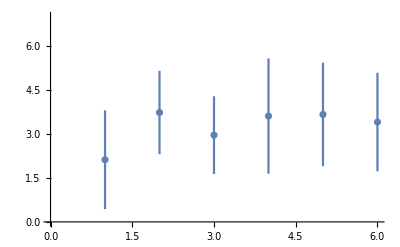

```mathematica
ErrorListPlot[Transpose[{castlesmean,castlesdev}],PlotRange->{Automatic,{0,7}}]
```

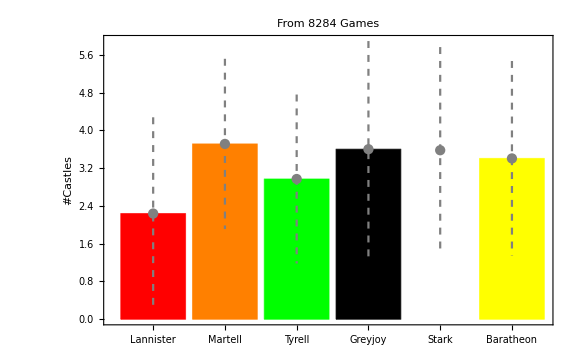

```mathematica
games2castles[list]
```

```mathematica
castles=<<"EndCastles.txt";
castlesmean=Mean[Cases[castles,{#,_Integer,_Integer,_Integer,_Integer,_Integer,_Integer}][[1,2;;7]]&/@pos];
```

```mathematica
ErrorBox
```

```mathematica
ST=Transpose[castlesStark][[2]]+Transpose[castlesStark][[3]];
BA=Transpose[castlesBaratheon][[2]]+Transpose[castlesBaratheon][[3]];
MA=Transpose[castlesMartell][[2]]+Transpose[castlesMartell][[3]];
TY=Transpose[castlesTyrell][[2]]+Transpose[castlesTyrell][[3]];
GJ=Transpose[castlesGJ][[2]]+Transpose[castlesGJ][[3]];LA=Transpose[castlesLannister][[2]]+Transpose[castlesLannister][[3]];
```

```mathematica
STH=Histogram[ST,Automatic,"Probability",ChartStyle->White,Frame->True,FrameLabel->{"Points","# Games"},PlotLabel->"Stark"];
BAH=Histogram[BA,Automatic,"Probability",ChartStyle->Yellow,Frame->True,FrameLabel->{"Points","# Games"},PlotLabel->"Baratheon"];
TYH=Histogram[TY,Automatic,"Probability",ChartStyle->RGBColor[{0,0.6,0}],Frame->True,FrameLabel->{"Points","# Games"},PlotLabel->"Tyrell"];
MAH=Histogram[MA,Automatic,"Probability",ChartStyle->Orange,Frame->True,FrameLabel->{"Points","# Games"},PlotLabel->"Martell"];
GJH=Histogram[GJ,Automatic,"Probability",ChartStyle->Black,Frame->True,FrameLabel->{"Points","# Games"},PlotLabel->"Greyjoy"];
LAH=Histogram[LA,Automatic,"Probability",ChartStyle->RGBColor[{.9,0,0}],Frame->True,FrameLabel->{"Points","# Games"},PlotLabel->"Lannister"];
```

```mathematica
Rasterize[GraphicsGrid[{{STH,TYH},{BAH,GJH},{LAH,MAH}},Frame->True,PlotLabel->StringForm["Number of mustering points at the end of the game. Statistics: `` Games",Length[ST]]],RasterSize->800,ImageSize->800]
```

-Graphics-

```mathematica
nrs=Transpose[castlesStark][[1]];
```

```mathematica
nrs
```

```mathematica
ST//Length
```

7893

```mathematica
castlesBaratheon[[positionsGLalliance]]
```

{{90174,2,3},{90209,2,1},{90224,0,0},{90252,2,0},{90260,2,2},{90294,2,0},{90320,2,1},{90335,3,4},{90352,2,1},{90388,2,5},{90401,2,1},{90423,2,1},{90444,0,0},{90487,1,1},{90498,0,1},{90573,2,3},{90580,1,1},{90681,2,1},{90696,2,2},{90697,2,3},{90703,2,2},{90725,1,0},{90739,2,1},{90748,1,0},{90788,1,0},{90826,2,0},{90857,1,2},{90861,1,0},{90879,0,0},{90914,0,0},{90939,2,2},{90969,2,3},{90977,3,4},{90987,1,1},{90995,2,5},{90998,3,1},{91050,3,4},1877,{143518,3,1},{143555,2,1},{143575,2,2},{143579,2,1},{143693,2,2},{143699,2,4},{143718,1,1},{143738,2,1},{143768,2,3},{143788,2,1},{143792,3,4},{143863,2,2},{143880,0,1},{143889,2,1},{143950,2,2},{143978,0,1},{144005,2,2},{144083,3,1},{144085,2,1},{144104,0,0},{144118,0,0},{144130,3,4},{144145,2,1},{144176,2,1},{144200,2,0},{144209,2,3},{144229,2,5},{144310,2,2},{144374,2,1},{144405,1,0},{144470,2,5},{144501,2,3},{144560,2,5},{144566,2,1},{144673,2,5},{144685,2,1},{144705,1,0}}
 |  |  |  |

```mathematica
CastleMatrix=Join[{{"Nrs","Stark","Baratheon","Martell","Tyrell","Greyjoy","Lannister"}},Transpose[{nrs,ST,BA,MA,TY,GJ,LA}]]
```

{{Nrs,Stark,Baratheon,Martell,Tyrell,Greyjoy,Lannister},{90001,2,4,2,3,1,7},{90017,4,3,7,0,5,1},{90028,5,1,3,5,5,1},{90032,8,1,4,2,4,0},{90035,5,3,5,2,1,4},{90051,3,4,3,3,7,0},{90070,2,3,4,3,7,0},{90078,2,7,4,0,4,2},{90079,2,7,0,3,0,5},{90083,7,5,3,1,0,2},{90087,1,3,2,4,1,7},{90089,4,2,4,7,0,3},{90091,4,0,5,4,6,1},{90092,3,7,3,2,1,3},{90093,4,0,7,3,3,3},{90113,6,3,0,7,3,1},{90116,5,4,6,2,3,0},{90132,4,7,3,0,4,2},{90142,2,7,3,3,5,0},{90144,0,7,4,2,4,3},7852,{144685,2,3,7,0,4,4},{144695,4,5,4,1,5,1},{144698,7,0,4,3,3,3},{144705,5,1,5,4,4,1},{144714,5,2,4,2,7,0},{144717,7,6,3,3,1,0},{144736,1,6,5,1,0,7},{144753,6,3,0,7,3,1},{144772,3,4,3,3,7,0},{144778,0,3,4,2,7,4},{144780,5,3,7,0,2,2},{144783,7,4,4,2,3,0},{144808,4,4,2,1,2,7},{144812,0,4,4,2,7,3},{144815,3,4,4,7,0,0},{144824,6,4,6,0,4,0},{144825,0,7,4,3,4,2},{144847,7,2,3,4,1,3},{144879,3,0,5,5,7,0},{144890,4,4,7,0,5,0},{144900,4,2,4,3,0,7}}
 |  |  |  |

```mathematica
pos2castles[pos_]:=(
SetDirectory["C:\\Users\\Lion\\Documents\\My Projects\\GOT\\Extract txt\\Castles"];
castlesStark=Import["CastlesStark.txt","Table","FieldSeparators"->","][[pos]];
castlesMartell=Import["CastlesMartell.txt","Table","FieldSeparators"->","][[pos]];
castlesTyrell=Import["CastlesTyrell.txt","Table","FieldSeparators"->","][[pos]];
castlesGJ=Import["CastlesGJ.txt","Table","FieldSeparators"->","][[pos]];
castlesLannister=Import["CastlesLannister.txt","Table","FieldSeparators"->","][[pos]];
castlesBaratheon=Import["CastlesBaratheon.txt","Table","FieldSeparators"->","][[pos]];
ST=Transpose[castlesStark][[2]]+Transpose[castlesStark][[3]];
BA=Transpose[castlesBaratheon][[2]]+Transpose[castlesBaratheon][[3]];
MA=Transpose[castlesMartell][[2]]+Transpose[castlesMartell][[3]];
TY=Transpose[castlesTyrell][[2]]+Transpose[castlesTyrell][[3]];
GJ=Transpose[castlesGJ][[2]]+Transpose[castlesGJ][[3]];LA=Transpose[castlesLannister][[2]]+Transpose[castlesLannister][[3]];
STH=Histogram[ST,Automatic,"Probability",ChartStyle->White,Frame->True,FrameLabel->{"Points","# Games"},PlotLabel->"Stark"];
BAH=Histogram[BA,Automatic,"Probability",ChartStyle->Yellow,Frame->True,FrameLabel->{"Points","# Games"},PlotLabel->"Baratheon"];
TYH=Histogram[TY,Automatic,"Probability",ChartStyle->RGBColor[{0,0.6,0}],Frame->True,FrameLabel->{"Points","# Games"},PlotLabel->"Tyrell"];
MAH=Histogram[MA,Automatic,"Probability",ChartStyle->Orange,Frame->True,FrameLabel->{"Points","# Games"},PlotLabel->"Martell"];
GJH=Histogram[GJ,Automatic,"Probability",ChartStyle->Black,Frame->True,FrameLabel->{"Points","# Games"},PlotLabel->"Greyjoy"];
LAH=Histogram[LA,Automatic,"Probability",ChartStyle->RGBColor[{.9,0,0}],Frame->True,FrameLabel->{"Points","# Games"},PlotLabel->"Lannister"];
Rasterize[GraphicsGrid[{{STH,TYH},{BAH,GJH},{LAH,MAH}},Frame->True,PlotLabel->StringForm["Number of mustering points at the end of the game. Statistics: `` Games",Length[ST]]],RasterSize->800,ImageSize->800]
)
```

```mathematica
castlesStark[[Position[ST,7]//Flatten]]
```

{{90252,3,4},{90725,2,5},{90826,2,5},{90861,3,4},{91295,2,5},{91316,2,5},{91439,2,5},{91475,3,4},{91527,3,4},{91607,2,5},{91706,2,5},{92156,2,5},{92306,2,5},{92533,2,5},{92592,2,5},{92616,2,5},{92735,2,5},{92860,2,5},{93002,2,5},{93059,4,3},{93305,2,5},{93474,2,5},{93662,2,5},{93671,3,4},{93682,2,5},{93868,2,5},{93877,2,5},{93903,3,4},{93942,3,4},{93953,2,5},{94002,2,5},{94060,2,5},{94091,2,5},{94095,3,4},{94293,3,4},{94464,2,5},{94739,2,5},{94960,2,5},{95252,2,5},{95277,1,6},{95320,3,4},{95519,2,5},{95567,2,5},{95718,2,5},{96128,3,4},{96277,2,5},{96411,2,5},{96447,2,5},{96683,3,4},{96892,2,5},{97425,2,5},{97626,3,4},{97952,2,5},{98516,2,5},{98711,1,6},{99072,2,5},{99195,3,4},{99887,1,6},{99943,2,5},{99951,2,5},{99957,2,5},{100212,2,5},{100443,2,5},{100480,3,4},{100664,2,5},{100709,2,5},{100776,1,6},{100815,2,5},{100829,2,5},{100840,3,4},{100970,3,4},{100999,2,5},{101015,3,4},{101270,3,4},{101321,2,5},{101390,2,5},{101842,2,5},{101857,2,5},{101919,1,6},{102004,2,5},{102078,3,4},{102286,1,6},{102722,2,5},{102807,2,5},{102839,2,5},{103556,3,4},{104488,2,5},{104571,2,5},{104815,2,5},{104949,2,5},{104956,2,5},{105228,2,5},{105400,3,4},{105729,2,5},{106251,2,5},{106468,3,4},{106532,2,5},{106713,2,5},{106836,3,4},{107156,2,5},{107276,2,5},{107446,2,5},{107619,2,5},{107783,1,6},{108046,2,5},{108246,2,5},{108403,3,4},{108656,2,5},{108773,2,5},{108908,2,5},{108982,2,5},{109037,2,5},{109359,2,5},{109439,2,5},{109589,2,5},{109663,2,5},{109896,3,4},{110011,2,5},{110053,2,5},{110514,2,5},{110583,2,5},{110726,2,5},{110797,1,6},{110993,2,5},{111007,2,5},{111142,3,4},{111206,2,5},{111237,3,4},{111460,3,4},{111477,2,5},{111648,2,5},{111926,2,5},{112098,2,5},{113065,2,5},{113243,2,5},{113578,2,5},{114100,2,5},{114183,4,3},{114286,3,4},{115327,1,6},{115416,2,5},{115422,2,5},{115740,3,4},{115911,2,5},{116091,2,5},{116100,3,4},{116117,2,5},{116153,2,5},{117096,2,5},{117697,1,6},{117787,2,5},{118162,2,5},{118199,2,5},{118526,2,5},{118571,2,5},{118656,2,5},{119071,2,5},{119202,2,5},{119467,3,4},{119526,2,5},{119572,2,5},{119711,2,5},{119781,4,3},{119807,3,4},{120090,3,4},{120101,2,5},{120122,2,5},{120166,3,4},{120275,2,5},{120639,1,6},{121134,2,5},{121322,3,4},{121658,3,4},{121765,3,4},{121831,2,5},{121955,2,5},{122692,3,4},{122737,2,5},{122857,2,5},{123208,1,6},{123369,3,4},{123809,2,5},{123927,2,5},{124200,2,5},{124288,2,5},{124303,2,5},{124468,2,5},{124813,1,6},{125062,3,4},{125139,2,5},{125481,2,5},{125584,2,5},{125647,1,6},{125714,2,5},{125721,2,5},{125869,6,1},{125917,3,4},{125929,2,5},{126098,2,5},{126244,3,4},{126308,1,6},{126419,2,5},{126505,2,5},{126645,2,5},{126780,2,5},{126810,2,5},{127410,3,4},{127420,2,5},{127758,1,6},{127764,2,5},{127818,3,4},{128032,2,5},{128356,2,5},{128373,3,4},{128390,3,4},{128428,3,4},{128571,2,5},{128673,2,5},{128730,2,5},{128884,3,4},{128885,2,5},{129048,2,5},{129094,3,4},{129875,2,5},{129895,2,5},{129951,1,6},{130020,2,5},{130220,2,5},{130449,2,5},{130528,3,4},{130533,1,6},{130872,2,5},{130882,2,5},{131044,2,5},{131163,3,4},{131561,2,5},{131676,2,5},{131948,3,4},{132049,2,5},{132076,2,5},{132134,2,5},{132297,2,5},{132491,2,5},{132620,3,4},{132762,2,5},{132852,3,4},{133075,2,5},{133087,2,5},{133349,2,5},{133378,3,4},{133885,2,5},{134351,2,5},{134385,2,5},{134519,2,5},{134642,3,4},{134855,2,5},{135046,3,4},{135067,3,4},{135270,2,5},{135920,2,5},{135926,3,4},{136152,2,5},{136189,2,5},{136215,2,5},{136231,2,5},{136686,2,5},{136729,2,5},{136862,2,5},{136878,2,5},{137309,2,5},{137331,1,6},{137471,2,5},{137596,3,4},{137648,3,4},{137679,3,4},{138003,3,4},{138617,2,5},{138637,2,5},{139187,3,4},{139304,2,5},{139535,2,5},{139608,4,3},{139907,2,5},{139913,3,4},{140115,2,5},{140143,4,3},{140383,2,5},{140468,2,5},{141523,2,5},{141791,3,4},{142183,3,4},{142249,1,6},{142528,3,4},{142694,2,5},{142720,2,5},{142960,3,4},{143287,3,4},{143693,2,5},{143978,2,5},{144083,2,5},{144310,2,5},{144566,2,5}}

```mathematica
pos2castles[starkopening]
```

-Graphics-

```mathematica
ref=pos2castles[;;];
```

```mathematica
Row[{pos2castles[starkopening],ref}]
```

-Graphics--Graphics-

## List of games where something happened

List where Martell was extinguished:

```mathematica
Transpose[castlesLannister[[Position[TY,14]//Flatten]]][[1]]
```

{93369,105625}